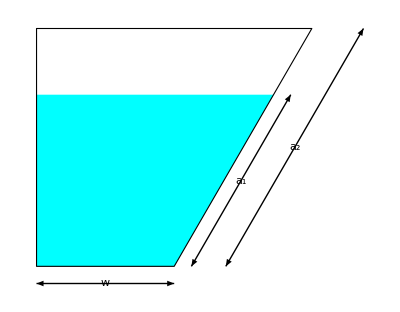

```mathematica
Module[{θ,a2,h1,h2,w,δ,w1,w2},
θ=60°;a2=8;
h1=5;h2=a2*Sin[θ];w=4;
δ=0.5;

w1=w+h1/Sin[θ]*Cos[θ];w2=w+h2/Sin[θ]*Cos[θ];

Graphics[{
{FaceForm@Cyan,Polygon[{{0,h1},{0,0},{w,0},{w1,h1}}]},
{EdgeForm@Thick,FaceForm@None,Polygon[{{0,h2},{0,0},{w,0},{w2,h2}}]} ,
{Arrowheads@{-0.05,0.05},
Arrow[{{0,-δ},{w,-δ}}],Arrow[{{w+δ,0},{w1+δ,h1}}],Arrow[{{w+3*δ,0},{w2+3*δ,h2}}]},
Text[Framed[Style[#1,17],Background->White,FrameStyle->None,FrameMargins->Tiny],#2]&@@@{{Style["w",Italic],{0.5*w,-δ}},{Subscript[Style["a",Italic],1],{w+w1+2*δ,h1}/2},{Subscript[Style["a",Italic],2],{w+w2+6*δ,h2}/2}}
}]
]
```

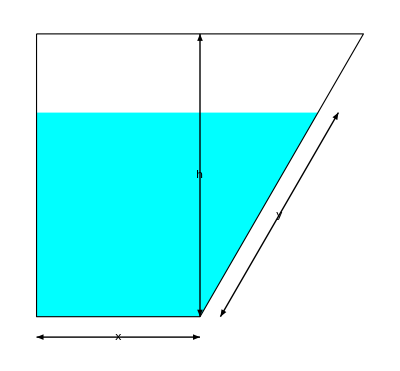

```mathematica
Module[{θ,a2,h1,h2,w,δ,w1,w2},
θ=60°;a2=8;
h1=5;h2=a2*Sin[θ];w=4;
δ=0.5;

w1=w+h1/Sin[θ]*Cos[θ];w2=w+h2/Sin[θ]*Cos[θ];

Graphics[{
{FaceForm@Cyan,Polygon[{{0,h1},{0,0},{w,0},{w1,h1}}]},
{EdgeForm@Thick,FaceForm@None,Polygon[{{0,h2},{0,0},{w,0},{w2,h2}}]} ,
{Arrowheads@{-0.05,0.05},
Arrow[{{0,-δ},{w,-δ}}],Arrow[{{w,0},{w,h2}}],Arrow[{{w+δ,0},{w1+δ,h1}}]},
Text[Framed[Style[#1,Italic,17],Background->White,FrameStyle->None,FrameMargins->Tiny],#2]&@@@{{"x",{0.5*w,-δ}},(*{"h",{w,0.5*h2}},*){"y",{w+w1+2*δ,h1}/2}},
Text[Framed[Style["h",Italic,17],Background->Cyan,FrameStyle->None,FrameMargins->Tiny],{w,0.5*h2}]
}]
]
```